Model Figure 2A

Kinetic model of the network

```mathematica
odes2a={
X'[t]==v1-v2,
YP'[t]==v3-v4,
RP'[t]==v5-v6
};
rates2a={
v1->k0+k1*S,
v2->k2*X[t]+k2p*RP[t]*X[t],
v3->(k3*X[t]*(YT-YP[t]))/(Km3+YT-YP[t]),
v4->(k4*YP[t])/(Km4+YP[t]),
v5->(k5*YP[t]*(RT-RP[t]))/(Km5+RT-RP[t]),
v6->(k6*RP[t])/(Km6+RP[t])
};
param2a={
k0->0,
k1->1,
k2->0.01,
k2p->10,
k3->0.1,
k4->0.2,
k5->0.1,
k6->0.05,
YT->1,
RT->1,
Km3->0.01,
Km4->0.01,
Km5->0.01,
Km6->0.01};
```

```mathematica
Timesol2a=NDSolve[Join[odes2a/.rates2a/.param2a/.S->2,{X[0]==5,YP[0]==0.5,RP[0]==0}],{X,YP,RP},{t,0,75}];
```

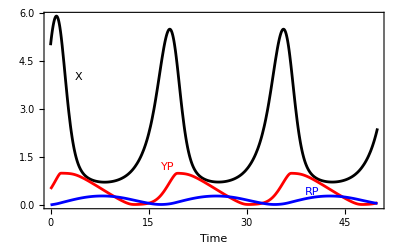

```mathematica
Plot[Evaluate[{X[t],YP[t],RP[t]}/.Timesol2a],{t,0,50},PlotRange->All,PlotStyle->{{Black,Thickness[0.005]},{Red,Thickness[0.005]},{Blue,Thickness[0.005]}},Frame->True,FrameLabel->{"Time",""},BaseStyle->{FontSize->14},Epilog->{Black,Text["X",{4.25,4}],Red,Text["YP",{18,1.2}],Blue,Text["RP",{40,0.4}]}]
```

Calculation of the unstable steady state

```mathematica
ss=FindRoot[odes2a/.rates2a/.param2a/.{X'[t]->0,YP'[t]->0,RP'[t]->0}/.S->2,{{X[t],2},{YP[t],1},{RP[t],0.2}}]
odes2a[[All,2]]/.rates2a/.param2a/.S->2/.ss
```

{X[t]→1.99359,YP[t]→0.459307,RP[t]→0.0993218}

{2.88658×10^-15,2.77556×10^-17,0.}

Determination of the eigenvalues at the unstable steady state

```mathematica
JacMat=D[odes2a[[All,2]]/.rates2a/.param2a,{{X[t],YP[t],RP[t]}}];
MatrixForm[JacMat]
JacMat/.ss
Eigenvalues[%]
```

(-0.01-10 RP[t] | 0 | -10 X[t]
(0.1 (1-YP[t]))/(1.01-YP[t]) | (0.1 X[t] (1-YP[t]))/(1.01-YP[t])^2-(0.1 X[t])/(1.01-YP[t])+(0.2 YP[t])/(0.01+YP[t])^2-0.2/(0.01+YP[t]) | 0
0 | (0.1 (1-RP[t]))/(1.01-RP[t]) | (0.05 RP[t])/(0.01+RP[t])^2-0.05/(0.01+RP[t])+(0.1 (1-RP[t]) YP[t])/(1.01-RP[t])^2-(0.1 YP[t])/(1.01-RP[t]))

{{-1.00322,0,-19.9359},{0.0981841,-0.0156544,0},{0,0.0989019,-0.0423905}}

{-1.15573,0.0472357+0.407244 ⅈ,0.0472357-0.407244 ⅈ}

So, indeed an oscillatory state: positive eigenvalues with non-negative real parts

Model Figure 2B

Kinetic model of the network

```mathematica
G[u_,v_,J_,K_]:=(2*u*K)/(v-u+v*J+u*K+√((v-u+v*J+u*K)^2-4*(v-u)*u*K))
```

```mathematica
odes2b={
R'[t]==v1-v2,
X'[t]==v5-v6
};
rates2b={
v1->k0*EP+k1*S,
v2->k2*R[t]+k2p*R[t]*X[t],
v5->k5*R[t],
v6->k6*X[t]
}/.EP->G[k3*R[t],k4,J3,J4];
param2b={
k0->4,
k1->1,
k2->1,
k2p->1,
k3->1,
k4->1,
k5->0.1,
k6->0.075,
J3->0.3,
J4->0.3};
```

```mathematica
Timesol2b=NDSolve[Join[odes2b/.rates2b/.param2b/.S->0.2,{X[0]==1,R[0]==0.8}],{X,R},{t,0,150}];
```

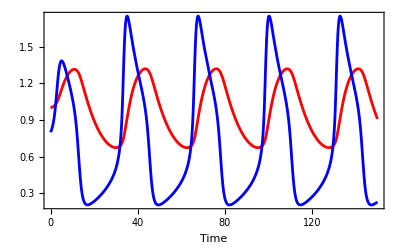

```mathematica
Plot[Evaluate[{X[t],R[t]}/.Timesol2b],{t,0,150},PlotStyle->{{Red,Thickness[0.005]},{Blue,Thickness[0.005]}},Frame->True,FrameLabel->{"Time",""},BaseStyle->{FontSize->14}]
```

Calculation of the unstable steady state

```mathematica
ss=FindRoot[odes2b/.{R'[t]->0,X'[t]->0}/.rates2b/.param2b/.S->0.2,{{X[t],1},{R[t],0.7}}]
odes2b[[All,2]]/.rates2b/.param2b/.S->0.2/.ss
```

{X[t]→0.983216,R[t]→0.737412}

{3.33067×10^-16,0.}

```mathematica
PlA=ParametricPlot[Evaluate[{X[t],R[t]}/.Timesol2b],{t,80,150},PlotRange->{{0,1.5},{0,3}},Frame->True,FrameLabel->{"X","R"},BaseStyle->{FontSize->14},PlotStyle->{{Black,Thickness[0.005]}},AspectRatio->1,Epilog->{Black,PointSize[0.025],Point[{X[t],R[t]}/.ss]}];
```

```mathematica
Rnullcline2b=Solve[0==v1-v2/.rates2b/.param2b/.S->0.2,{R[t]}];
Xnullcline2b=Solve[0==v5-v6/.rates2b/.param2b/.S->0.2,{R[t]}];
```

```mathematica
PlB=Plot[{R[t]/.Rnullcline2b[[1]],R[t]/.Rnullcline2b[[2]],R[t]/.Rnullcline2b[[3]],R[t]/.Xnullcline2b[[1]]},{X[t],0,1.5},Frame->True,FrameLabel->{"X","R"},BaseStyle->{FontSize->14},PlotStyle->{{Dashed,Red,Thickness[0.005]},{Red,Thickness[0.005]},{Red,Thickness[0.005]},{Blue,Thickness[0.005]}}];
```

```mathematica
plC=StreamPlot[{v5-v6/.rates2b/.param2b/.S->0.2,v1-v2/.rates2b/.param2b/.S->0.2},{X[t],0,1.5},{R[t],0,3},StreamStyle->Gray];
```

The middle plot of Figure 2B (note the axes change)

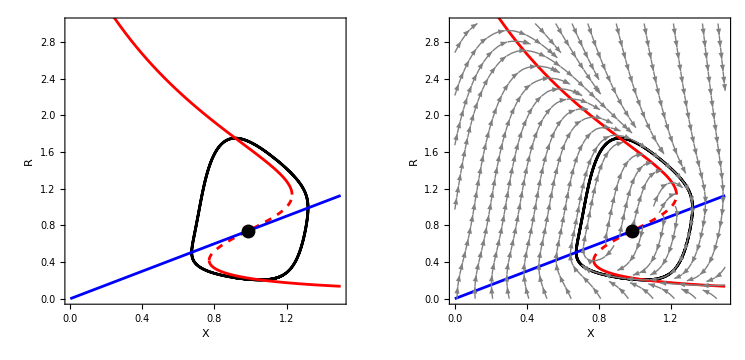

```mathematica
GraphicsGrid[{{Show[PlA,PlB],Show[PlA,PlB,plC]}}]
```

```mathematica
JacMat=D[odes2b[[All,2]]/.rates2b/.param2b/.S->0.2/.param2b,{{R[t],X[t]}}];
MatrixForm[JacMat/.ss]
Eigenvalues[JacMat/.ss]
JacMat[[1,1]]+JacMat[[2,2]]/.ss (* trace *)
Det[JacMat/.ss]
%>1/4 (%%)^2  (* so we have an unstable node *)
```

(0.743494 | -0.737412
0.1 | -0.075)

{0.64042,0.028074}

0.668494

0.0179792

False

Indeed an unstable steady state

Again the bifurcation diagram would require programming.

Model Figure 2C

Kinetic model of the network

```mathematica
odes2c={
X'[t]==v1-v2,
R'[t]==v3-v4
};
rates2c={
v1->k1*S,
v2->(k0p+k0*EP)*X[t],
v3->(k0p+k0*EP)*X[t],
v4->k2*R[t]
}/.EP->G[k3*R[t],k4,J3,J4];
param2c={
k0->0.4,
k0p->0.01,
k1->1,
k2->1,
k3->1,
k4->0.3,
J3->0.05,
J4->0.05};
```

```mathematica
Timesol2c=NDSolve[Join[odes2c/.rates2c/.param2c/.S->0.2,{X[0]==3,R[0]==0.2}],{X,R},{t,0,250}];
```

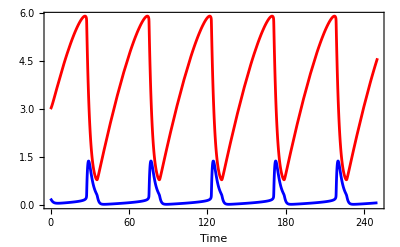

```mathematica
Plot[Evaluate[{X[t],R[t]}/.Timesol2c],{t,0,250},PlotStyle->{{Red,Thickness[0.005]},{Blue,Thickness[0.005]}},Frame->True,FrameLabel->{"Time",""},BaseStyle->{FontSize->14}]
```

```mathematica
PlA=ParametricPlot[Evaluate[{X[t],R[t]}/.Timesol2c],{t,100,250},PlotRange->{{0,7},{0,1.5}},Frame->True,FrameLabel->{"X","R"},BaseStyle->{FontSize->14},PlotStyle->{{Black,Thickness[0.005]}},AspectRatio->1];
```

```mathematica
Rnullcline2c=Solve[0==v1-v2/.rates2c/.param2c/.S->0.2,X[t]];
Xnullcline2c=Solve[0==v3-v4/.rates2c/.param2c/.S->0.2,X[t]];
```

```mathematica
PlB=ListLinePlot[{Table[{X[t]/.Rnullcline2c[[1]],R[t]},{R[t],0,7,0.01}],Table[{X[t]/.Xnullcline2c[[1]],R[t]},{R[t],0,7,0.01}]},PlotRange->{{0,7},{0,1.5}},PlotStyle->{{Blue,Thickness[0.005]},{Red,Thickness[0.005]}}];
```

```mathematica
PlC=StreamPlot[{v1-v2/.rates2c/.param2c/.S->0.2,v3-v4/.rates2c/.param2c/.S->0.2},{X[t],0,7},{R[t],0,1.5},StreamStyle->Gray];
```

The middle plot of Figure 2C (note the axes change)

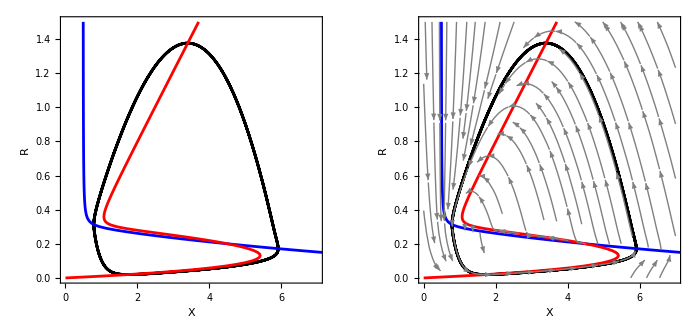

```mathematica
GraphicsGrid[{{Show[PlA,PlB],Show[PlA,PlB,PlC]}}]
```

Calculation of the unstable steady state

```mathematica
ss=FindRoot[odes2c/.{R'[t]->0,X'[t]->0}/.rates2c/.param2c/.S->0.2,{{X[t],1},{R[t],0.7}}]
odes2c[[All,2]]/.rates2c/.param2c/.S->0.2/.ss
```

{X[t]→4.50842,R[t]→0.2}

{2.77556×10^-17,-2.77556×10^-17}

(-(-(0.04 R[t] (-0.95+(-0.2 (0.3-R[t])-1.9 (0.315-0.95 R[t])+0.2 R[t])/(2 √((0.315-0.95 R[t])^2-0.2 (0.3-R[t]) R[t]))))/((0.315-0.95 R[t]+√((0.315-0.95 R[t])^2-0.2 (0.3-R[t]) R[t]))^2)+0.04/(0.315-0.95 R[t]+√((0.315-0.95 R[t])^2-0.2 (0.3-R[t]) R[t]))) X[t] | -0.01-(0.04 R[t])/(0.315-0.95 R[t]+√((0.315-0.95 R[t])^2-0.2 (0.3-R[t]) R[t]))
-1+(-(0.04 R[t] (-0.95+(-0.2 (0.3-R[t])-1.9 (0.315-0.95 R[t])+0.2 R[t])/(2 √((0.315-0.95 R[t])^2-0.2 (0.3-R[t]) R[t]))))/((0.315-0.95 R[t]+√((0.315-0.95 R[t])^2-0.2 (0.3-R[t]) R[t]))^2)+0.04/(0.315-0.95 R[t]+√((0.315-0.95 R[t])^2-0.2 (0.3-R[t]) R[t]))) X[t] | 0.01+(0.04 R[t])/(0.315-0.95 R[t]+√((0.315-0.95 R[t])^2-0.2 (0.3-R[t]) R[t])))

{-2.05506,0.0215864}

-2.03347

-0.0443614

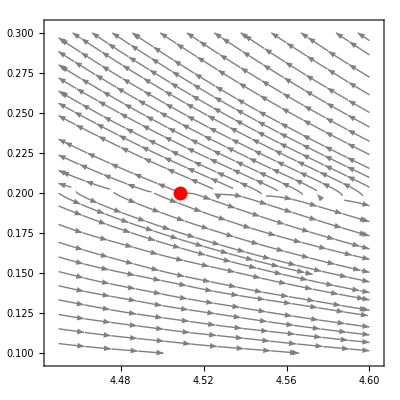

```mathematica
JacMat=D[odes2c[[All,2]]/.rates2c/.param2c/.S->0.2/.param2c,{{R[t],X[t]}}];
MatrixForm[JacMat]
Eigenvalues[JacMat/.ss]
JacMat[[1,1]]+JacMat[[2,2]]/.ss (* trace *)
Det[JacMat/.ss] (* we have a saddle point *)
StreamPlot[{v1-v2/.rates2c/.param2c/.S->0.2,v3-v4/.rates2c/.param2c/.S->0.2},{X[t],4.45,4.6},{R[t],0.1,0.3},StreamStyle->Gray,Epilog->{Red,PointSize[0.025],Point[{X[t],R[t]}/.ss]}]
```